```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

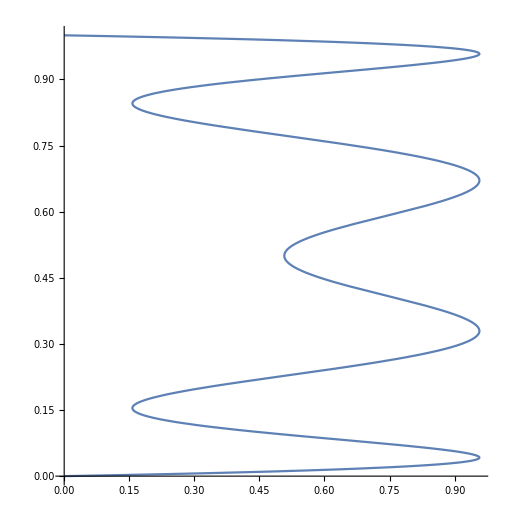

```mathematica
ParametricPlot[{real/.{y-> 0,μ-> 3.8283}, x} ,{x,0,1}]
```

```mathematica
map3[0.07,0,3.8283]
```

0.77794+0. ⅈ

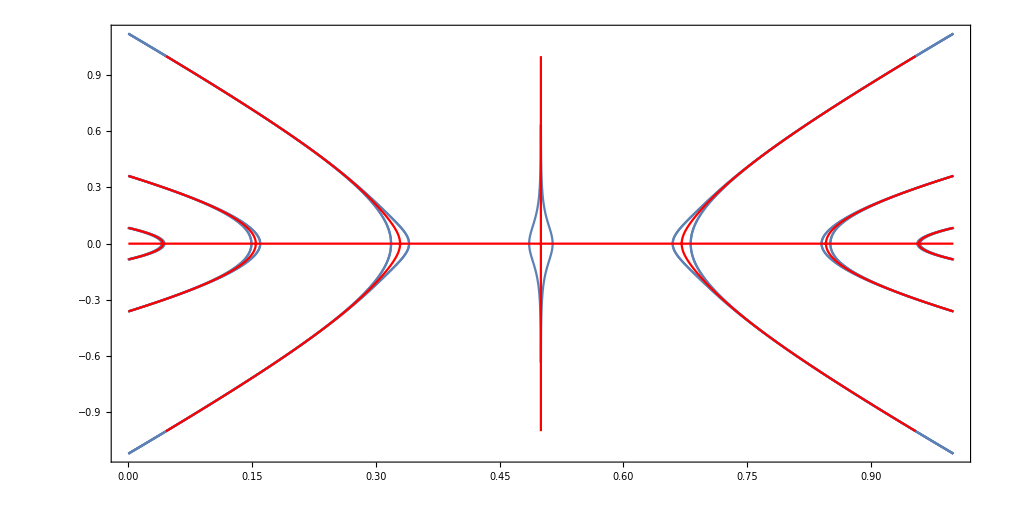
```mathematica
img4 = -Graphics-;
```

```mathematica
{{"0.04362","0.0006239"}}
```

```mathematica
{{"0.1598","-0.00004998"}}
```

```mathematica
{{"0.3402","0.00103"}}
```

```mathematica
{{"0.4858","-0.0005546"}}
```

```mathematica
ϵvalues = {0.04362-xbands⟦1⟧,0.1598-xbands⟦2⟧,0.3402-xbands⟦3⟧,-0.4858+0.5}
```

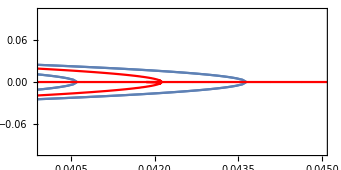

```mathematica
Show[img4,PlotRange-> {{0.04,0.045},{-0.1,0.1}}]
```

```mathematica
imaginary = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

```mathematica
mat = {{D[real,x],D[real,y]},{D[imaginary,x],D[imaginary,y]}};
```

```mathematica
linearmap[xn_,yn_,μi_]:=  mat.{xn,yn}/.{x-> xn,y-> yn, μ-> μi}
```

```mathematica
map3[0.1599344157699688,-0.0010557164917092967,3.82830] - 0.1599344157699688+0.0010557164917092967ⅈ
```

4.10783×10^-15+1.6675×10^-16 ⅈ

```mathematica
{{a,b},{c,d}} . {e,f}
```

{a e+b f,c e+d f}

```mathematica
linearmap[0.1599344157699688,-0.0010557164917092967,3.82830]
```

{0.159851,-0.0310753}

```mathematica
fixedpts= Solve[{(imaginary/.μ-> 3.82830) == y,(real/.μ-> 3.82830)== x},{x,y}, Reals]⟦All,All,2⟧
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0,0},{0.159934,-0.00105572},{0.159934,0.00105572},{0.514357,-0.00274882},{0.514357,0.00274882},{0.738787,0},{0.956315,-0.000302167},{0.956315,0.000302167}}

```mathematica
ys =FullSimplify[ Solve[imaginary==0,y]];
```

```mathematica
pmeio1[μ0_] := FindMinimum[{(real/.y-> ys⟦1,1,2⟧/.μ-> μ0),0.1≤x≤0.25}, x]
```

```mathematica
xcentro = thelistxf⟦1,1⟧[μ0];
```

```mathematica
xcentro =  pmeio1[3.8283]⟦1⟧;
```

```mathematica
xcentro
```

0.157276

```mathematica
xlist = (*Range[0,1,0.01]*) {0.1572759218008186};
ylist = Range[-0.01,0.01,0.00001];
ptslist = Outer[List,xlist,ylist]//Flatten[#,1]&;
(*ptslist = Outer[List,xlist,ylist]*)
```

```mathematica
ptslist
```

{{0.157276,-0.01},{0.157276,-0.00999},{0.157276,-0.00998},{0.157276,-0.00997},{0.157276,-0.00996},1991,{0.157276,0.00996},{0.157276,0.00997},{0.157276,0.00998},{0.157276,0.00999},{0.157276,0.01}}
 |  |  |  |

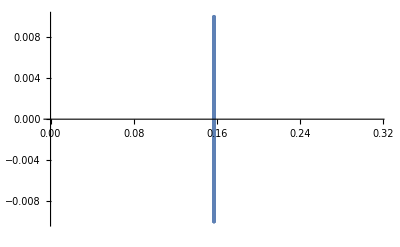

```mathematica
ListPlot[ptslist]
```

```mathematica
μ0 = 3.8283
listcomplex={};
For[i=0,i<Length[ptslist],i++;
xn=ptslist⟦i,1⟧;
yn=ptslist⟦i,2⟧;
For[n=0,n<3,n++;
{xnn,ynn} = {linearmap[xn,yn,μ0]⟦1⟧,linearmap[xn,yn,μ0]⟦2⟧};
If[Abs[xnn]>30 , Break[]];
xn = xnn;
yn = ynn];
If[Abs[xnn]>30 , AppendTo[listcomplex, {xn,yn}],AppendTo[listcomplex, {xn,yn}]]];
```

3.8283

```mathematica
listcomplex
```

{}

```mathematica
Show[ListPlot[listcomplex]]
```

-Graphics-

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
Reduce[xn1 == x μ-x^2 μ+y^2,y]
```

y==-√(xn1-x μ+x^2 μ)||y==√(xn1-x μ+x^2 μ)

```mathematica
Reduce[yn1 == y μ-2 x y μ,x]
```

(μ==0&&yn1==0)||(y μ≠0&&x==(-yn1+y μ)/(2 y μ))||(yn1==0&&μ≠0&&y==0)

```mathematica
yinv =Flatten[Solve[y==(-√(xn1-x μ+x^2 μ))/.x-> (-yn1+y μ)/(2 y μ), y],1]
```

{y→-(√(4 xn1-μ-√((16 yn1^2)/μ+(-4 xn1+μ)^2)))/(2 √2),y→(√(4 xn1-μ-√((16 yn1^2)/μ+(-4 xn1+μ)^2)))/(2 √2),y→-(√(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))/(2 √2),y→(√(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))/(2 √2)}

```mathematica
xinv = Solve[x==((-yn1+y μ)/(2 y μ))/.y->-(√(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))/(2 √2),x]
```

{{x→-(√2 (-yn1-(μ √(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))/(2 √2)))/(μ √(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))}}

```mathematica
mapxinv[xn1_,yn1_,μ_] :=-(√2 (-yn1-(μ √(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))/(2 √2)))/(μ √(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))
```

```mathematica
FullSimplify[-(√2 (-yn1-(μ √(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))/(2 √2)))/(μ √(4 xn1-μ+√((16 yn1^2)/μ+(-4 xn1+μ)^2)))]
```

(μ+(2 √2 yn1)/(√(4 xn1-μ+√((16 yn1^2+μ (-4 xn1+μ)^2)/μ))))/(2 μ)

```mathematica
((μ+(2 √2 yn1)/(√(4 xn1-μ-√((16 yn1^2+μ (-4 xn1+μ)^2)/μ))))/(2 μ))/.yn1-> 0.1
```

(μ+0.282843/(√(4 xn1-μ-√((0.16+μ (-4 xn1+μ)^2)/μ))))/(2 μ)

```mathematica
FullSimplify[(2 √2 yn1)/(√(4 xn1-μ-√((16 yn1^2+μ (-4 xn1+μ)^2)/μ)))]
```

(2 √2 yn1)/(√(4 xn1-μ-√((16 yn1^2+μ (-4 xn1+μ)^2)/μ)))

```mathematica
(2 √2 yn1)/(√(4 xn1-μ-√((16 yn1^2+μ (-4 xn1+μ)^2)/μ)))/.{xn1-> 0.3,μ-> 3.8284,yn1-> 0.01}
```

0.-0.0123362 ⅈ

```mathematica
map[45/100,1/10,38284/10000]
```

985813/1000000+(9571 ⅈ)/250000

```mathematica
mapxinv[985813/1000000,9571/250000,38284/10000]
```

-(2500 √(2/(28713/250000+(√1207276369)/250000)) (-9571/250000-(9571 √(1/2 (28713/250000+(√1207276369)/250000)))/5000))/9571

```mathematica
PDF[NormalDistribution[xbands⟦1⟧,0.03],x]/(100PDF[NormalDistribution[xbands⟦1⟧,0.03],xbands⟦1⟧])
```

0.01 ⅇ^(-555.556 (-0.0415067+x)^2)

```mathematica
xs = Solve[imaginary==0,x];
xbands = Sort[xs/.{y-> 0,μ-> μ0}]⟦All,1,2⟧
```

{0.0421228,0.154466,0.329308,1/2,0.670692,0.845534,0.957877}

```mathematica
ϵvalues = {0.04362-xbands⟦1⟧,0.1598-xbands⟦2⟧,0.3402-xbands⟦3⟧,-0.4858+0.5}
```

{0.00149721,0.00533397,0.0108925,0.0142}

```mathematica
μ0=3.8283
```

3.8283

```mathematica
xlist1 = Range[xbands⟦1⟧ - ϵvalues⟦1⟧, xbands⟦1⟧ + ϵvalues⟦1⟧, (2 ϵvalues⟦1⟧)/150]; 
ylist1 = Range[-0.01,0.01,0.0001];
ptslist1 = Outer[List,xlist1,ylist1]//Flatten[#,1]&;

ylistgauss1 = Table[PDF[NormalDistribution[xbands⟦1⟧,ϵvalues⟦1⟧/3],x]/(500PDF[NormalDistribution[xbands⟦1⟧,ϵvalues⟦1⟧/3],xbands⟦1⟧]),{x,xlist1}];
ptsgauss1 =Flatten[Table[Table[{xlist1⟦i⟧,j},{j,Range[-ylistgauss1⟦i⟧,ylistgauss1⟦i⟧, 0.00001]}],{i,Range[1,Length[xlist1]]}],1];
```

```mathematica
ylistgauss1;
```

```mathematica
ptsgauss1⟦1,2⟧
```

0.

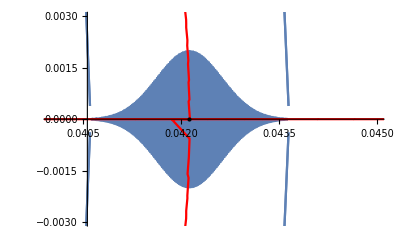

```mathematica
Show[ListPlot[ptsgauss1],img4, Graphics[Point[{xbands⟦1⟧,0}]], PlotRange-> {{0.04,0.045},{-0.003,0.003}}]
```

```mathematica
PDF[NormalDistribution[xbands⟦1⟧,0.01],xbands⟦1⟧-0.1]
```

7.6946×10^-21

```mathematica
μ0 = 3.8283;
listcomplex1={};
For[i=0,i<Length[ptsgauss1],i++;
xn=ptsgauss1⟦i,1⟧;
yn=ptsgauss1⟦i,2⟧;
For[n=0,n<3,n++;
{xnn,ynn} = {Re[map[xn,yn,μ0]],Im[map[xn,yn,μ0]]};
If[Abs[xnn]>30 , Break[]];
xn = xnn;
yn = ynn];
If[Abs[xnn]>30 , None,AppendTo[listcomplex1, {xn,yn}]]];
```

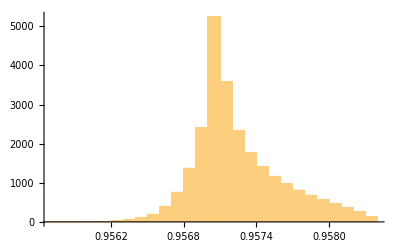

```mathematica
Histogram[listcomplex1⟦All,1⟧,5000]
```

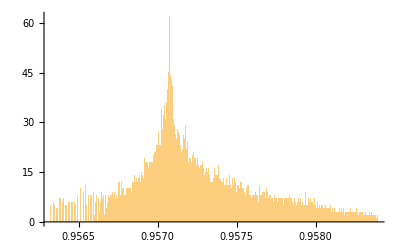

```mathematica
Histogram[listcomplex1⟦All,1⟧,5000]
```

```mathematica
Length[xlist2]
```

151

```mathematica
xlist2 = Range[xbands⟦2⟧ - ϵvalues⟦1⟧, xbands⟦2⟧ + ϵvalues⟦1⟧, (2ϵvalues⟦1⟧)/150];
ylist2 = Range[-0.01,0.01,0.0001];
ptslist2 = Outer[List,xlist2,ylist2]//Flatten[#,1]&;

ylistgauss2 = Table[PDF[NormalDistribution[xbands⟦2⟧,ϵvalues⟦1⟧/3],x]/(500PDF[NormalDistribution[xbands⟦2⟧,ϵvalues⟦1⟧/3],xbands⟦2⟧]),{x,xlist2}];
ptsgauss2 =Flatten[Table[Table[{xlist2⟦i⟧,j},{j,Range[-ylistgauss2⟦i⟧,ylistgauss2⟦i⟧, 0.00001]}],{i,Range[1,Length[xlist2]]}],1];
```

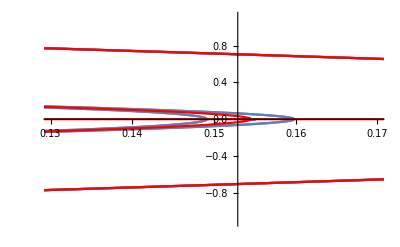

```mathematica
Show[ListPlot[ptsgauss2],img4, PlotRange-> {{0.13,0.17},Automatic}]
```

```mathematica
μ0 = 3.8283;
listcomplex2={};
For[i=0,i<Length[ptsgauss2],i++;
xn=ptsgauss2⟦i,1⟧;
yn=ptsgauss2⟦i,2⟧;
For[n=0,n<3,n++;
{xnn,ynn} = {Re[map[xn,yn,μ0]],Im[map[xn,yn,μ0]]};
If[Abs[xnn]>30 , Break[]];
xn = xnn;
yn = ynn];
If[Abs[xnn]>30 , None,AppendTo[listcomplex2, {xn,yn}]]];
```

```mathematica
xlist3 = Range[xbands⟦3⟧ - ϵvalues⟦1⟧, xbands⟦3⟧ + ϵvalues⟦1⟧, (2ϵvalues⟦1⟧)/150];
ylist3 = Range[-0.01,0.01,0.0001];
ptslist3 = Outer[List,xlist3,ylist3]//Flatten[#,1]&;

ylistgauss3 = Table[PDF[NormalDistribution[xbands⟦3⟧,ϵvalues⟦1⟧/3],x]/(500PDF[NormalDistribution[xbands⟦3⟧,ϵvalues⟦1⟧/3],xbands⟦3⟧]),{x,xlist3}];
ptsgauss3 =Flatten[Table[Table[{xlist3⟦i⟧,j},{j,Range[-ylistgauss3⟦i⟧,ylistgauss3⟦i⟧, 0.00001]}],{i,Range[1,Length[xlist3]]}],1];
```

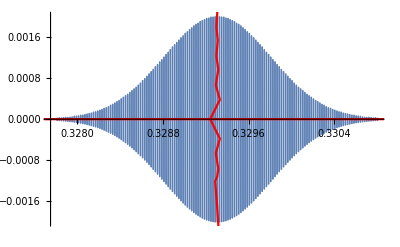

```mathematica
Show[ListPlot[ptsgauss3],img4]
```

```mathematica
μ0 = 3.8283;
listcomplex3={};
For[i=0,i<Length[ptsgauss3],i++;
xn=ptsgauss3⟦i,1⟧;
yn=ptsgauss3⟦i,2⟧;
For[n=0,n<3,n++;
{xnn,ynn} = {Re[map[xn,yn,μ0]],Im[map[xn,yn,μ0]]};
If[Abs[xnn]>30 , Break[]];
xn = xnn;
yn = ynn];
If[Abs[xnn]>30 , None,AppendTo[listcomplex3, {xn,yn}]]];
```

```mathematica
xlist4 = Range[xbands⟦4⟧ - ϵvalues⟦1⟧, xbands⟦4⟧ + ϵvalues⟦1⟧, (2ϵvalues⟦1⟧)/150];
ylist4 = Range[-0.01,0.01,0.0001];
ptslist4 = Outer[List,xlist4,ylist4]//Flatten[#,1]&;

ylistgauss4 = Table[PDF[NormalDistribution[xbands⟦4⟧,ϵvalues⟦1⟧/3],x]/(500PDF[NormalDistribution[xbands⟦4⟧,ϵvalues⟦1⟧/3],xbands⟦4⟧]),{x,xlist4}];
ptsgauss4 =Flatten[Table[Table[{xlist4⟦i⟧,j},{j,Range[-ylistgauss4⟦i⟧,ylistgauss4⟦i⟧, 0.00001]}],{i,Range[1,Length[xlist4]]}],1];
```

```mathematica
μ0 = 3.8283;
listcomplex4={};
For[i=0,i<Length[ptsgauss4],i++;
xn=ptsgauss4⟦i,1⟧;
yn=ptsgauss4⟦i,2⟧;
For[n=0,n<3,n++;
{xnn,ynn} = {Re[map[xn,yn,μ0]],Im[map[xn,yn,μ0]]};
If[Abs[xnn]>30 , Break[]];
xn = xnn;
yn = ynn];
If[Abs[xnn]>30 , None,AppendTo[listcomplex4, {xn,yn}]]];
```

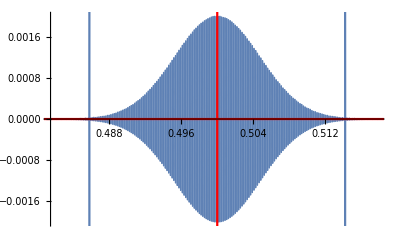

```mathematica
Show[ListPlot[ptsgauss4],img4]
```

```mathematica
s
```

```mathematica
StandardDeviation[listcomplex1]
```

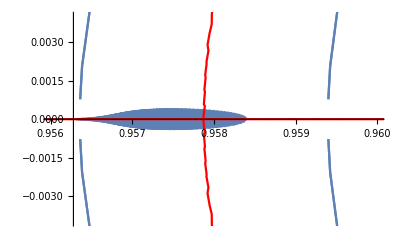

```mathematica
Show[ListPlot[listcomplex1],img4, PlotRange-> {{0.956,0.96},{-0.004,0.004}}]
```

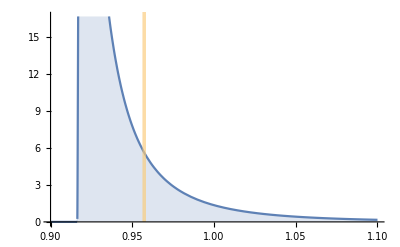

```mathematica
Show[Plot[PDF[dist1,x],{x,0.9,1.1}, Filling->Axis, PlotRange->Automatic],Histogram[listcomplex1⟦All,1⟧,{0.9,1.1,1/10000}]]
```

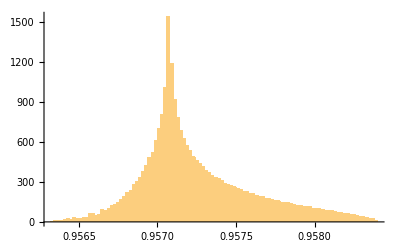

```mathematica
Histogram[listcomplex1⟦All,1⟧,80]
```

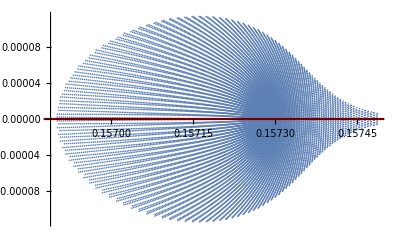

```mathematica
Show[ListPlot[listcomplex2],img4]
```

```mathematica
Plot[PDF[dist2,x],{x,0,0.2}, Filling->Axis, PlotRange->Automatic]
```

JohnsonDistribution::posprm: Parameter -0.823396 at position 3 in JohnsonDistribution[SB,3.45034,-0.823396,0.0247201,0.157226] is expected to be positive.

General::stop: Further output of JohnsonDistribution::posprm will be suppressed during this calculation.

-Graphics-

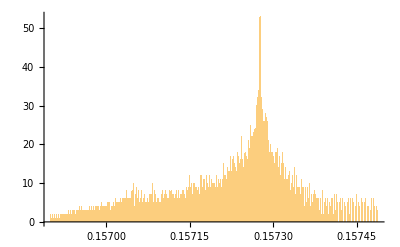

```mathematica
Histogram[listcomplex2⟦All,1⟧,5000]
```

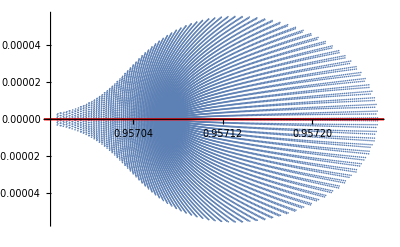

```mathematica
Show[ListPlot[listcomplex3],img4]
```

```mathematica
Plot[PDF[dist3,x],{x,0.9,1.1}, Filling->Axis, PlotRange->Automatic]
```

JohnsonDistribution::posprm: Parameter -2.25402 at position 3 in JohnsonDistribution[SB,9.09879,-2.25402,0.914929,0.956519] is expected to be positive.

General::stop: Further output of JohnsonDistribution::posprm will be suppressed during this calculation.

-Graphics-

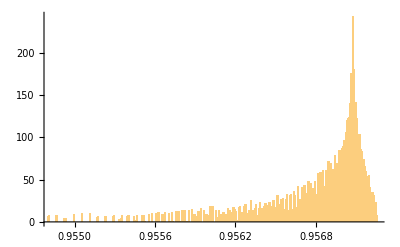

```mathematica
Histogram[listcomplex3⟦All,1⟧,5000]
```

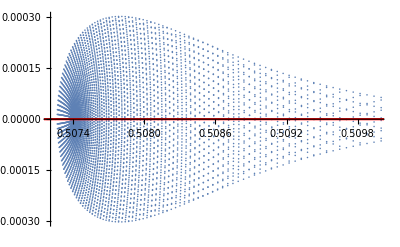

```mathematica
Show[ListPlot[listcomplex4],img4]
```

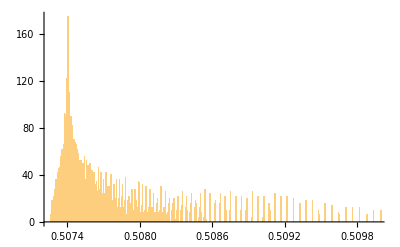

```mathematica
Histogram[listcomplex4⟦All,1⟧,5000]
```

Range do xlist fixo em 0.03:

```mathematica
s1 =StandardDeviation[listcomplex1]
```

{0.000361126,0.000167184}

```mathematica
s2=StandardDeviation[listcomplex2]
```

{0.000102841,0.0000475692}

```mathematica
s3=StandardDeviation[listcomplex3]
```

{0.0000501922,0.000023216}

```mathematica
s4 =StandardDeviation[listcomplex4]
```

{0.0000385556,0.0000178331}

Range do xlist dependente de ϵ:

```mathematica
s1 =StandardDeviation[listcomplex1]
```

{0.000361126,0.000167184}

```mathematica
s2=StandardDeviation[listcomplex2]
```

{0.000437253,0.00016944}

```mathematica
s3=StandardDeviation[listcomplex3]
```

{0.000821168,0.000168814}

```mathematica
s4 =StandardDeviation[listcomplex4]
```

{0.0010605,0.000168957}

```mathematica
sratio = {(4 s1⟦1⟧)/ϵvalues⟦1⟧,(4s2⟦1⟧)/ϵvalues⟦2⟧,(4s3⟦1⟧)/ϵvalues⟦3⟧,(4s4⟦1⟧)/ϵvalues⟦4⟧};
```

```mathematica
ϵvalueslog =Log[ϵvalues]
```

{-2.1346,-1.68249,-1.24801}

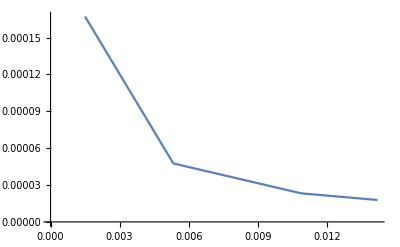

```mathematica
ListPlot[{{ϵvalues⟦1⟧,s1⟦2⟧},{ϵvalues⟦2⟧,s2⟦2⟧},{ϵvalues⟦3⟧,s3⟦2⟧},{ϵvalues⟦4⟧,s4⟦2⟧}}, Joined->True]
```

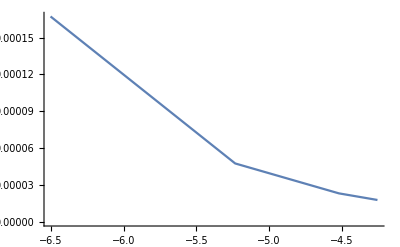

```mathematica
ListPlot[{{Log[ϵvalues⟦1⟧],s1⟦2⟧},{Log[ϵvalues⟦2⟧],s2⟦2⟧},{Log[ϵvalues⟦3⟧],s3⟦2⟧},{Log[ϵvalues⟦4⟧],s4⟦2⟧}}, Joined->True]
```

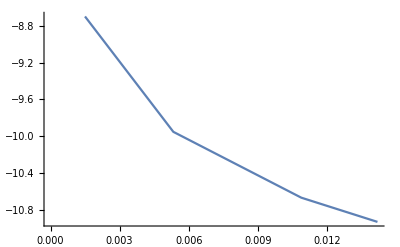

```mathematica
ListPlot[{{ϵvalues⟦1⟧,Log[s1⟦2⟧]},{ϵvalues⟦2⟧,Log[s2⟦2⟧]},{ϵvalues⟦3⟧,Log[s3⟦2⟧]},{ϵvalues⟦4⟧,Log[s4⟦2⟧]}}, Joined-> True]
```

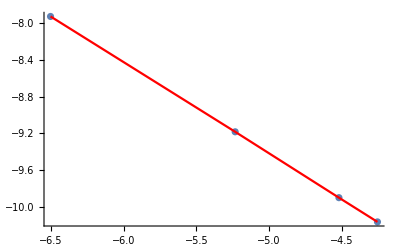

```mathematica
Show[ListPlot[{{Log[ϵvalues⟦1⟧],Log[s1⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[s2⟦1⟧]},{Log[ϵvalues⟦3⟧],Log[s3⟦1⟧]},{Log[ϵvalues⟦4⟧],Log[s4⟦1⟧]}} ],ListPlot[{{Log[ϵvalues⟦1⟧],Log[s1⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[s2⟦1⟧]},{Log[ϵvalues⟦3⟧],Log[s3⟦1⟧]},{Log[ϵvalues⟦4⟧],Log[s4⟦1⟧]}} ,Joined-> True, PlotStyle-> Red]]
```

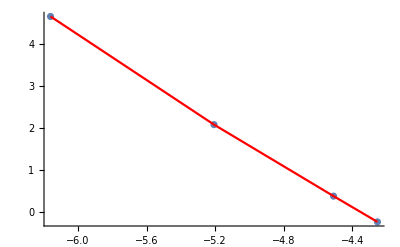

```mathematica
Show[ListPlot[{{Log[ϵvalues⟦1⟧],Log[sratio⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[sratio⟦2⟧]},{Log[ϵvalues⟦3⟧],Log[sratio⟦3⟧]},{Log[ϵvalues⟦4⟧],Log[sratio⟦4⟧]}}],ListPlot[{{Log[ϵvalues⟦1⟧],Log[sratio⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[sratio⟦2⟧]},{Log[ϵvalues⟦3⟧],Log[sratio⟦3⟧]},{Log[ϵvalues⟦4⟧],Log[sratio⟦4⟧]}}, Joined-> True, PlotStyle->Red]]
```

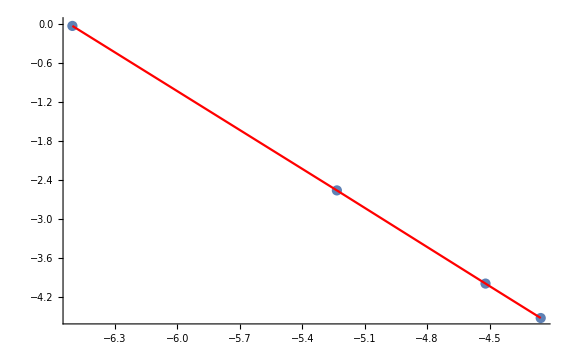

```mathematica
Show[ListPlot[{{Log[ϵvalues⟦1⟧],Log[sratio⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[sratio⟦2⟧]},{Log[ϵvalues⟦3⟧],Log[sratio⟦3⟧]},{Log[ϵvalues⟦4⟧],Log[sratio⟦4⟧]}}],ListPlot[{{Log[ϵvalues⟦1⟧],Log[sratio⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[sratio⟦2⟧]},{Log[ϵvalues⟦3⟧],Log[sratio⟦3⟧]},{Log[ϵvalues⟦4⟧],Log[sratio⟦4⟧]}}, Joined-> True, PlotStyle->Red]]
```

Limitando gaussianas pela distância máxima da borda da banda:

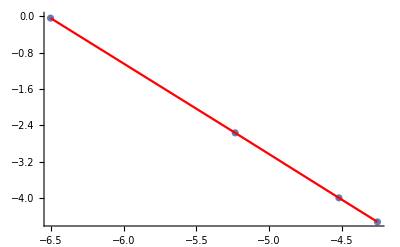

```mathematica
Show[ListPlot[{{Log[ϵvalues⟦1⟧],Log[sratio⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[sratio⟦2⟧]},{Log[ϵvalues⟦3⟧],Log[sratio⟦3⟧]},{Log[ϵvalues⟦4⟧],Log[sratio⟦4⟧]}}],ListPlot[{{Log[ϵvalues⟦1⟧],Log[sratio⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[sratio⟦2⟧]},{Log[ϵvalues⟦3⟧],Log[sratio⟦3⟧]},{Log[ϵvalues⟦4⟧],Log[sratio⟦4⟧]}}, Joined-> True, PlotStyle->Red]]
```

Lei de Potência

```mathematica
sdata =Partition[Riffle[ϵvalues,{s1⟦1⟧,s2⟦1⟧,s3⟦1⟧,s4⟦1⟧}],2];
attractiondata =Partition[Riffle[ϵvalues,sratio],2];
```

```mathematica
powerlaw = a x^k
```

a x^k

```mathematica
sfit=FindFit[sdata, powerlaw, {k,a}, x]
```

{k→-0.991649,a→5.70927×10^-7}

```mathematica
attracfit=FindFit[attractiondata, powerlaw, {k,a}, x]
```

{k→-1.98961,a→2.31388×10^-6}

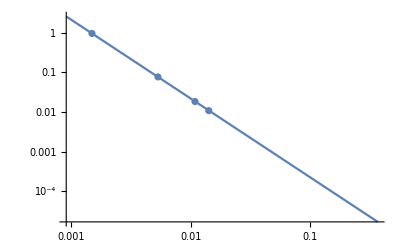

```mathematica
Show[LogLogPlot[powerlaw/.attracfit,{x,ⅇ^-7,ⅇ^-1}],ListPlot[{{Log[ϵvalues⟦1⟧],Log[sratio⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[sratio⟦2⟧]},{Log[ϵvalues⟦3⟧],Log[sratio⟦3⟧]},{Log[ϵvalues⟦4⟧],Log[sratio⟦4⟧]}}]]
```

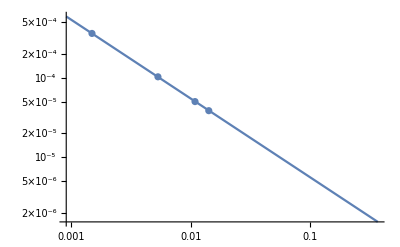

```mathematica
Show[LogLogPlot[powerlaw/.sfit,{x,ⅇ^-7,ⅇ^-1}],ListPlot[{{Log[ϵvalues⟦1⟧],Log[s1⟦1⟧]},{Log[ϵvalues⟦2⟧],Log[s2⟦1⟧]},{Log[ϵvalues⟦3⟧],Log[s3⟦1⟧]},{Log[ϵvalues⟦4⟧],Log[s4⟦1⟧]}} ]]
```

```mathematica
powerlaw/.sfit
```

(5.70927×10^-7)/x^0.991649

```mathematica
FindFit[{{2,1},{3,2},{4,3},{5,4}},a x + b, {a,b},x]
```

{a→1.,b→-1.}

Poder de Atração

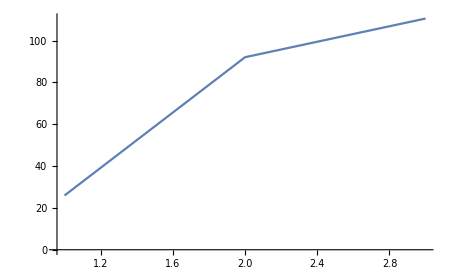

```mathematica
ListPlot[{{1,2/sratio⟦2⟧},{2,1/sratio⟦4⟧},{3,2/sratio⟦3⟧+2/sratio⟦1⟧}}, Joined->True]
```

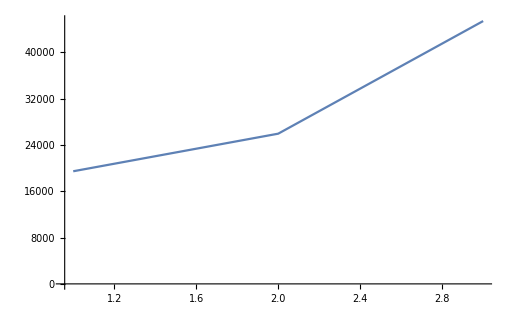

```mathematica
ListPlot[{{1,2/s2⟦1⟧},{2,1/s4⟦1⟧},{3,2/s3⟦1⟧+2/s1⟦1⟧}}, Joined->True]
```

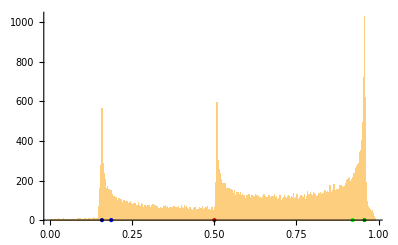
```mathematica
hist = -Graphics-;
```

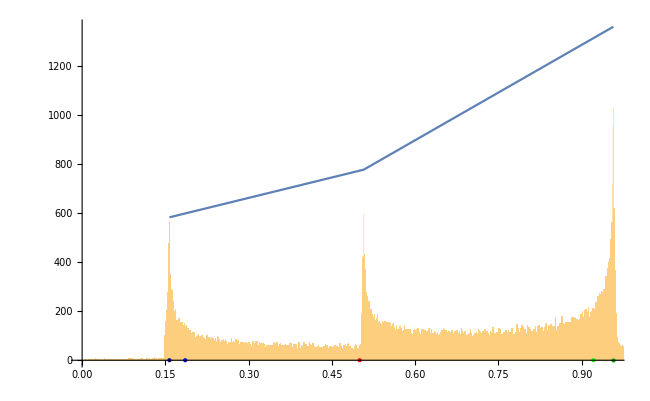

```mathematica
f = 0.03;
Show[ListPlot[{{0.1572759218008186,f 2/s2⟦1⟧},{0.5074039373682595,f 1/s4⟦1⟧},{0.9570750000148109,f(2/s3⟦1⟧+2/s1⟦1⟧)}}, Joined->True],hist]
```

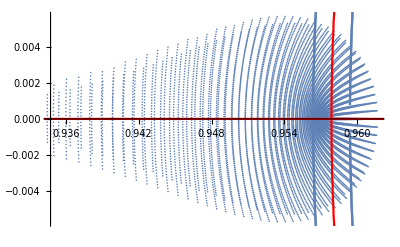

```mathematica
Show[ListPlot[listcomplex3],img4]
```

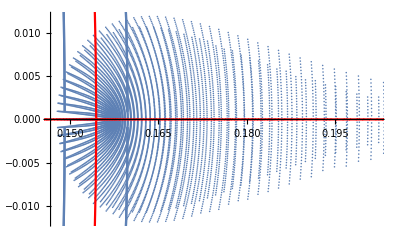

```mathematica
Show[ListPlot[listcomplex2],img4]
```

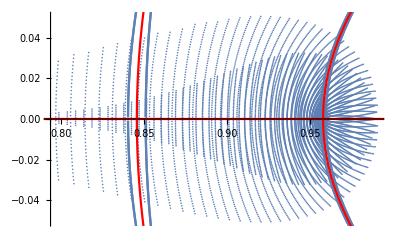

```mathematica
Show[ListPlot[listcomplex1],img4]
```

```mathematica
Mean[l1]
```

0.957249

```mathematica
Skewness[l3]
```

-2.25402

```mathematica
{l1,l2,l3,l4} = {listcomplex1⟦All,1⟧,listcomplex2⟦All,1⟧,listcomplex3⟦All,1⟧,listcomplex4⟦All,1⟧};
```

```mathematica
dist1
```

Function[x,Piecewise[{{(0.314247 ⅇ^(-1/2 (3.45005+0.822879 Log[(-0.916326+x)/(1.87357-x)])^2))/((1.87357-x) (-0.916326+x)), 0.916326<x<1.87357}, {0, True}}],Listable]

```mathematica
Mean[l1]
```

0.957249

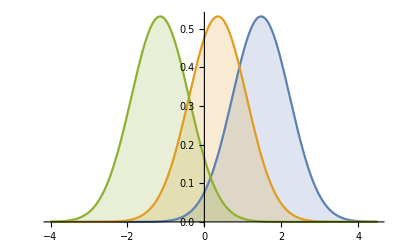

```mathematica
Plot[Table[PDF[JohnsonDistribution["SN",γ,2,1.1,1.5],x],{γ,{-0.5,1,3}}]//Evaluate,{x,-4,4.5},Filling->Axis]
```

```mathematica
JohnsonDistribution
```

```mathematica
{eq1,eq2,eq3,eq4}=Table[Moment[JohnsonDistribution["SN",a,b,c,d],i],{i,{1,2,3,4}}]
```

{(b c-a d)/b,(b^2 c^2-2 a b c d+d^2+a^2 d^2)/b^2,((b c-a d) (b^2 c^2-2 a b c d+3 d^2+a^2 d^2))/b^3,(b^4 c^4-4 a b^3 c^3 d+6 b^2 c^2 d^2+6 a^2 b^2 c^2 d^2-12 a b c d^3-4 a^3 b c d^3+3 d^4+6 a^2 d^4+a^4 d^4)/b^4}

```mathematica
FullSimplify[eq3/(eq2 eq1)]
```

(b^2 c^2-2 a b c d+(3+a^2) d^2)/(b^2 c^2-2 a b c d+(1+a^2) d^2)

```mathematica
Moment[l1,4]
```

0.839654

```mathematica
NSolve
```

```mathematica
b
```

b

```mathematica
Find
```

```mathematica
Solve[{eq1== Moment[l1,1], eq3== Moment[l1,3]},{a,b,c,d}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→-2769.03 d,c→1.15193×10^-23 (8.30996×10^22-3.13506×10^19 a)},{b→2769.03 d,c→1.15193×10^-23 (8.30996×10^22+3.13506×10^19 a)}}

```mathematica
Solve[{eq1== Moment[l1,1], eq4== Moment[l1,4]},{a,b,c,d}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→(1.9662×10^-33 (3.59631×10^32 √(-1. d^2)-3.75692×10^32 c √(-1. d^2)))/d,b→-0.738686 √(-d^2)},{a→(1.9662×10^-33 (-3.59631×10^32 √(-1. d^2)+3.75692×10^32 c √(-1. d^2)))/d,b→0.738686 √(-d^2)},{a→(1.9662×10^-33 (1.34804×10^36 √(d^2)-1.40824×10^36 c √(d^2)))/d,b→-2768.89 √(d^2)},{a→(1.9662×10^-33 (-1.34804×10^36 √(d^2)+1.40824×10^36 c √(d^2)))/d,b→2768.89 √(d^2)}}

```mathematica
Solve[{eq1== Moment[l1,1], eq2== Moment[l1,2]},{a,b,c,d}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→2.88049×10^-16 (3.32322×10^15-1.25367×10^12 a),d→-0.000361118 b},{c→2.88049×10^-16 (3.32322×10^15+1.25367×10^12 a),d→0.000361118 b}}

```mathematica
NSolve[{eq1== Moment[l1,1], eq2== Moment[l1,2],eq3== Moment[l1,3],eq4== Moment[l1,4]},{a,b,c,d},Method->"Homotopy"]
```

{}

```mathematica
dist1 = JohnsonDistribution["SB",Kurtosis[l1], Skewness[l1],Moment[l1,2],Mean[l1]];
```

```mathematica
dist2 =JohnsonDistribution["SB",Kurtosis[l2], Skewness[l2],Moment[l2,2],Mean[l2]];
```

```mathematica
dist3 = JohnsonDistribution["SB",Kurtosis[l3], Skewness[l3],Moment[l3,2],Mean[l3]];
```

```mathematica
dist4 = JohnsonDistribution["SB",Kurtosis[l4], Skewness[l4],Moment[l4,2],Mean[l4]];
```

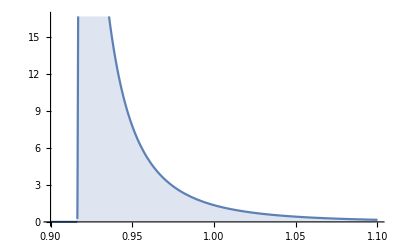

```mathematica
Plot[PDF[dist1,x],{x,0.9,1.1}, Filling->Axis, PlotRange->Automatic]
```

```mathematica
ys =FullSimplify[ Solve[im==0,y]]
```

{{y→0},{y→-(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→-(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→-(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)}}

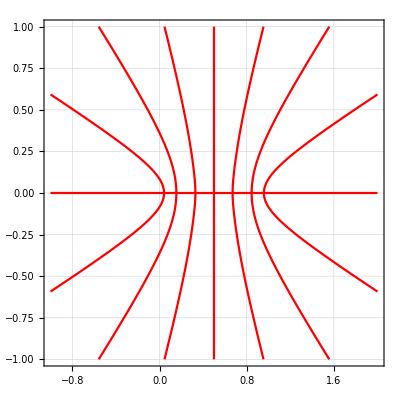

```mathematica
imμ =im/.μ-> μ0;
ContourPlot[imμ== 0,{x,-1,2},{y,-1,1},GridLines->Automatic, MaxRecursion->5, ContourStyle->Red]
```

```mathematica
ContourPlot
```

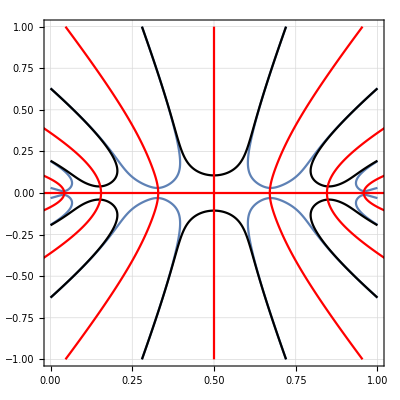

```mathematica
reμ =real/.μ-> μ0;
imμ = imaginary/.μ-> μ0;
Show[ContourPlot[reμ== 1,{x,0,1},{y,-1,1},GridLines->Automatic, MaxRecursion->5], ContourPlot[reμ== 0,{x,0,1},{y,-1,1},GridLines->Automatic, MaxRecursion->5, ContourStyle->Black],ContourPlot[imμ== 0,{x,-1,2},{y,-1,1},GridLines->Automatic, MaxRecursion->5, ContourStyle->Red]]
```

```mathematica
ys
```

{{y→0},{y→-(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→-(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→-(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)}}

```mathematica
D[(imaginary/.x-> x+ϵ)/. ys⟦4,1⟧,ϵ]/.{ϵ-> 0.01,x-> xbands⟦1⟧,μ-> 3.8283}
```

4.43138

```mathematica
D[(imaginary/.x-> x+ϵ)/. ys⟦2,1⟧,ϵ]/.{ϵ-> 0.01,x-> xbands⟦2⟧,μ-> 3.8283}
```

1.69546+0. ⅈ

```mathematica
D[(imaginary/.x-> x+ϵ)/. ys⟦6,1⟧,ϵ]/.{ϵ-> 0.01,x-> xbands⟦3⟧,μ-> 3.8283}
```

0.851435

```mathematica
Det[{{a,b},{c,d}}]
```

-b c+a d

```mathematica
Wronskian[{ⅇ^(a x),x ⅇ^(b x)},x]
```

ⅇ^((a+b) x) (1-a x+b x)

```mathematica
D[x ⅇ^(b x),x]
```

ⅇ^(b x)+b ⅇ^(b x) x